```mathematica
(*Алгаритм Грэхама*)
PolygonBilder[points_]:=Block[{
P = List[],
Pl = List[],Pr = List[],
Sl = List[], Sr= List[],
PlPoint , PrPoint,
length,n,
result
},
length = Length[points];
PlPoint = Part[points,1];
PrPoint =Part[points,1];

(*находим минимумальную и максимальную по иксам точку*)
For[n = 2, n ≤  length,++n,

If[Part[Part[points,n],1]<Part[PlPoint,1],PlPoint =Part[points,n]];
If[Part[Part[points,n],1]>Part[PrPoint,1],PrPoint =Part[points,n]];
];

(*делим множество на два подмножества*)
For[n = 1, n ≤  length,++n,
If[Part[points, n]== PlPoint ||Part[points, n]== PrPoint,,
If[Det[{PrPoint-PlPoint,Part[points, n]-PlPoint }]<0,AppendTo[Pr,Part[points, n]], AppendTo[Pl,Part[points, n]]]
];
];

(*вернем точки а то не хо*)
AppendTo[Pr, PlPoint];
AppendTo[Pl, PrPoint];


(*упорядочиваем*)
Pr = SortBy[Pr, First];
Pl= SortBy[Pl, First];
(*построение выпуклой оболочки для множества Pl*)
length = Length[Pl];
AppendTo[Sl, PlPoint];
For[n = 1, n ≤  length,++n,
If[Length[Sl]== 1,AppendTo[Sl,Part[Pl,n]],
If[Det[{Part[Sl, Length[Sl]]-Part[Sl, Length[Sl]-1],Part[Pl, n]-Part[Sl, Length[Sl]-1] }]≤ 0,
 AppendTo[Sl,Part[Pl,n]];,
 Sl = Delete[Sl, Length[Sl]]; n--;
];
];
];
(*построение выпуклой оболочки для множества Pr*)
length = Length[Pr];
AppendTo[Sr, PrPoint];
For[n = length,   1≤ n,--n,
If[Length[Sr]== 1,AppendTo[Sr,Part[Pr,n]],
If[Det[{Part[Sr, Length[Sr]]-Part[Sr, Length[Sr]-1],Part[Pr, n]-Part[Sr, Length[Sr]-1] }]< 0,
 AppendTo[Sr,Part[Pr,n]];,
 Sr = Delete[Sr, Length[Sr]]; n++;
];
];
];


Sr = Delete[Sr, 1];
result = Join[Sl,Sr];


Return[result]]
```

```mathematica
KickPoints[polygon_]:=Block[{
},
Return[Complement[points,polygon]]
]
```

```mathematica
Test[p1_,p2_,p3_,p4_] := Block[{
result,
α, β, k
},
α =((p2[[1]]-p1[[1]])*(p4[[1]]-p1[[1]]) +(p2[[2]]-p1[[2]])*(p4[[2]]-p1[[2]]));
β =((p2[[1]]-p3[[1]])*(p4[[1]]-p3[[1]]) +(p2[[2]]-p3[[2]])*(p4[[2]]-p3[[2]]));

If[α>0 &&β > 0, result =True,
If[α<0 &&β < 0, result =False,
k = Abs[(p2[[1]]-p1[[1]])*(p4[[2]]-p1[[2]])-(p4[[1]]-p1[[1]])*(p2[[2]]-p1[[2]])]*β 
+ α* Abs[(p2[[1]]-p3[[1]])*(p4[[2]]-p3[[2]])-(p4[[1]]-p3[[1]])*(p2[[2]]-p3[[2]])];
result = k≥0;
];
];

Return[result]
]

Flip[index_] :=Block[{
segmentN,
triangle1,triangle2,
t1i,t2i,
temp1,temp2
},
t1i =st[[index]][[1]];
t2i = st[[index]][[2]];
triangle1 = triangles[[t1i]];
triangle2 = triangles[[t2i]];

triangle1 = Complement[triangle1,{index}];
triangle2 = Complement[triangle2,{index}];

Print[triangle1];
Print[triangle2];

temp1 = Intersection[segments[[triangle1[[1]]]],segments[[triangle1[[2]]]]];
temp2 = Intersection[segments[[triangle2[[1]]]],segments[[triangle2[[2]]]]];

segmentN ={Flatten[temp1,1], Flatten[temp2,1]};
(*по индексу присваиваем сегмент*)

temp1 = triangle1;
temp2 =triangle2;
If[ Length[Intersection[segments[[triangle2[[1]]]],segments[[triangle1[[2]]]]]]== 1
,
triangle1 = {temp1[[1]],temp2[[2]],index};
triangle2 = {temp2[[1]],temp1[[2]],index};
,
triangle1 = {temp1[[1]],temp2[[1]],index};
triangle2 = {temp2[[2]],temp1[[2]],index};
];

Print[triangle1];
Print[triangle2];
Print[segmentN];

]
```

```mathematica
Triangulation[] := Block[{
polygon,
pointsN,
result,

i,leng
},
polygon = PolygonBilder[points];
pointsN =KickPoints[polygon];

leng = Length[polygon];
For[i = 1, i < leng,i++,
AppendTo[segments,{polygon[[i]],polygon[[i+1]]}];
];
AppendTo[segments,{polygon[[leng]],polygon[[1]]}];

For[i=1, i ≤  leng, i++,
AppendTo[segments,{polygon[[i]],pointsN[[1]]}];
];

For[i=1, i <  leng, i++,
AppendTo[triangles,{i, leng+i, leng+i+1}];
];
AppendTo[triangles,{i, leng*2, leng+1}];

For[i=1, i ≤ leng, i++,
AppendTo[st,{i}];
];
AppendTo[st,{leng,1}];
For[i=2, i ≤  leng, i++,
AppendTo[st,{i-1,i}];
];

Print[segments];
Print[triangles];
Print[st];
Return[result]
]
```

{{{7,595},{8,713}},{{8,713},{471,873}},{{471,873},{891,893}},{{891,893},{962,11}},{{962,11},{339,32}},{{339,32},{130,85}},{{130,85},{7,595}},{{7,595},{7,595}},{{7,595},{114,429}},{{8,713},{114,429}},{{471,873},{114,429}},{{891,893},{114,429}},{{962,11},{114,429}},{{339,32},{114,429}},{{130,85},{114,429}},{{7,595},{114,429}}}

{{1,9,10},{2,10,11},{3,11,12},{4,12,13},{5,13,14},{6,14,15},{7,15,16},{8,16,9}}

{{1},{2},{3},{4},{5},{6},{7},{8},{8,1},{1,2},{2,3},{3,4},{4,5},{5,6},{6,7},{7,8}}

result

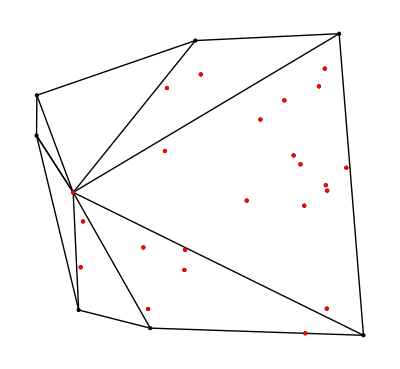

```mathematica
points= Table[{RandomInteger[{0, 1000}],RandomInteger[{0, 1000}]},{30}];
segments= List[];
triangles= List[];
st= List[];
Triangulation[]
Graphics[{Line[segments], Point[points],Red, Point[KickPoints[PolygonBilder[points]]]}]
```

```mathematica
Graphics[{Line[segments]}];
CreateTr[triangles];
Flip[11]
```

{2,10}

{3,12}

{2,3,11}

{12,10,11}

{{8,713},{891,893}}